```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=8.6173324*10^-3;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
cPlotData=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
zPlotData=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
V[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]
V[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[1,12,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
(*Zirconium*)
V[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[2,12,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]

(*Note these normalised potentials are not actually used in this book - I simply use the normal mass of C and Zr and define omega0 as that of th harmonic system*)
(*I want to 'normalise' to make the Hamiltonian as simple as possible - should I normalise 1) with respect to the harmonic fitted prefractor, 2) with respect to the first derivitive of the potential, 3) with respect to the species mass in AMU. If I want to let omega=1, then it can't be 3), it has to 1 or 2*)
Vnorm[1,2,x_]:=V[1,2,x]/V[1,2,x][[1]]
Vnorm[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]/V[1,2,x][[1]]
Vnorm[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]/V[1,2,x][[1]]
Vnorm[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]/V[1,2,x][[1]]
Vnorm[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]/V[1,2,x][[1]]
(*Normalised Zr potentials*)
Vnorm[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]/V[2,2,x][[1]]
Vnorm[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]/V[2,2,x][[1]]
Vnorm[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]/V[2,2,x][[1]]
Vnorm[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]/V[2,2,x][[1]]
Vnorm[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]/V[2,2,x][[1]]
```

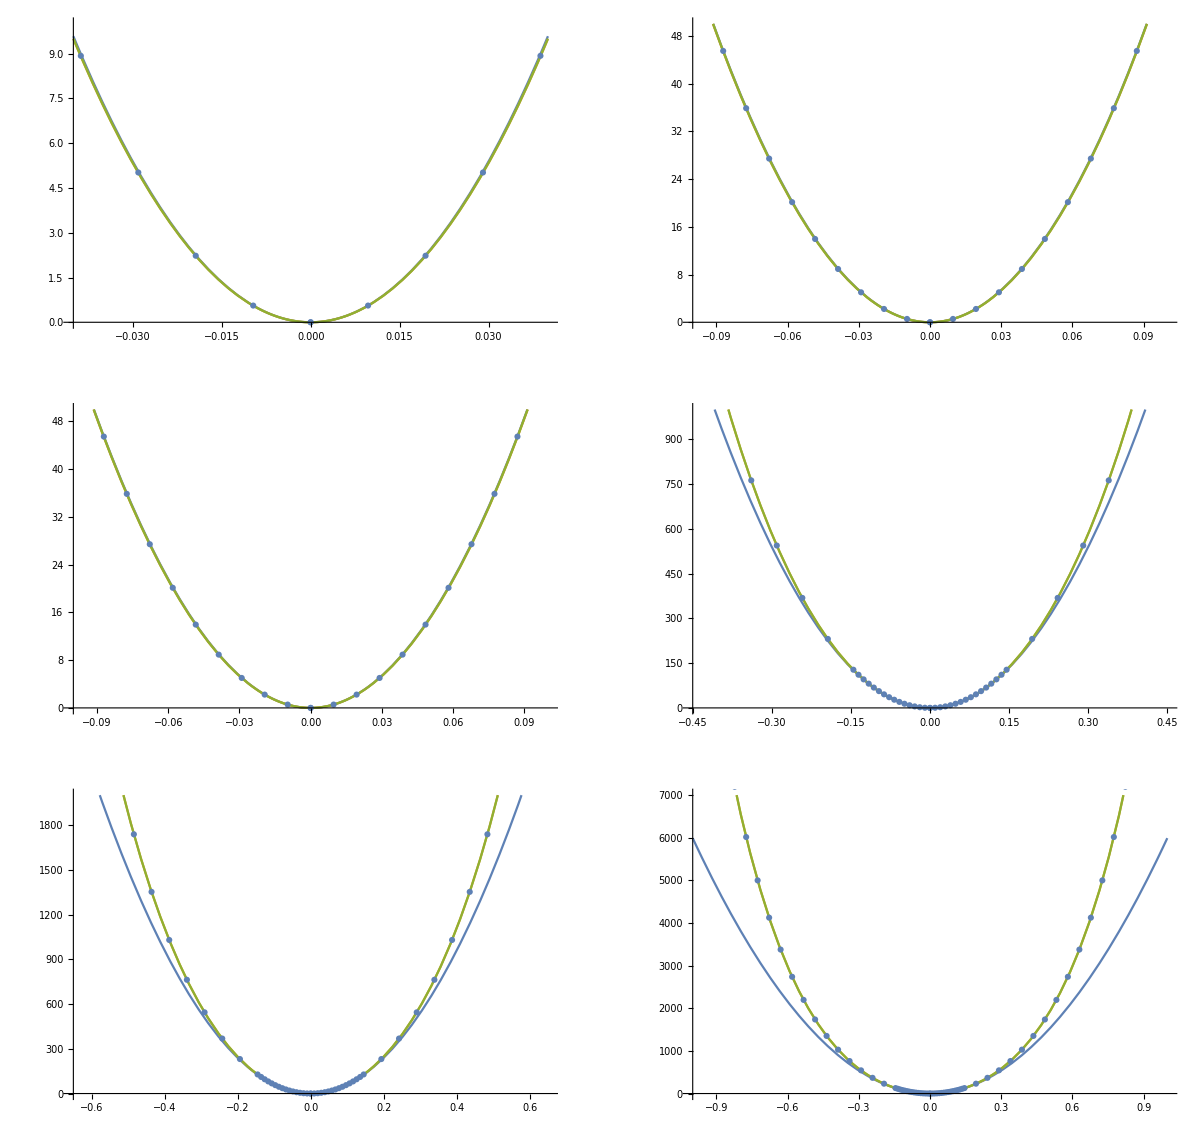

```mathematica
Carbon- look at fits at different scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@cPlotData],Show[P0,ListPlot@cPlotData]},{Show[P1,ListPlot@cPlotData],Show[P2,ListPlot@cPlotData]},{Show[P3,ListPlot@cPlotData],Show[P4,ListPlot@cPlotData]}},ImageSize->1200]
```

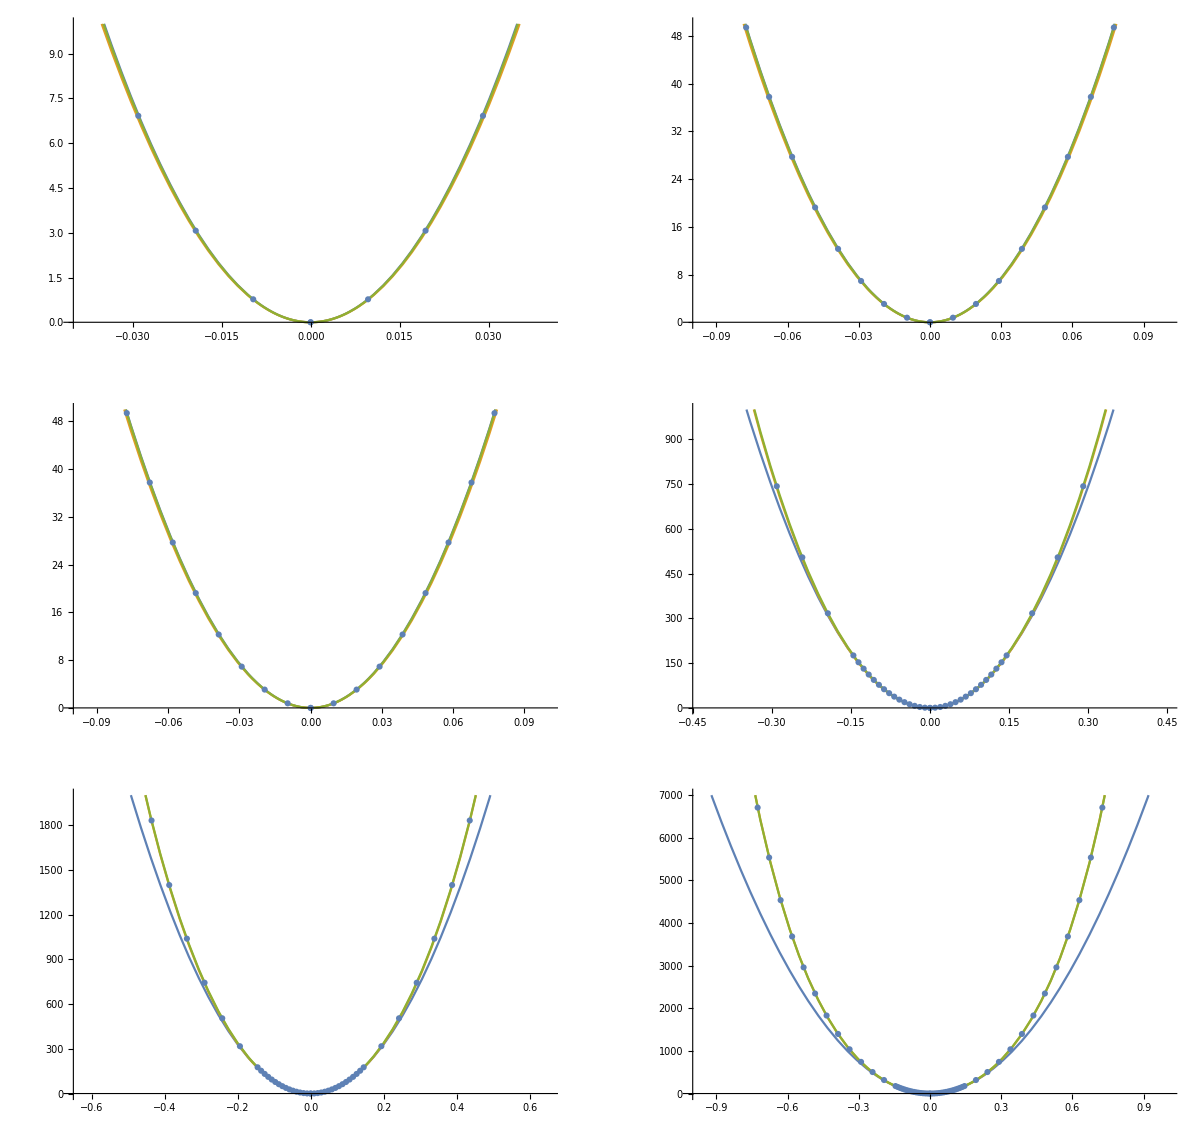

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@zPlotData],Show[P0z,ListPlot@zPlotData]},{Show[P1z,ListPlot@zPlotData],Show[P2z,ListPlot@zPlotData]},{Show[P3z,ListPlot@zPlotData],Show[P4z,ListPlot@zPlotData]}},ImageSize->1200]
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit as root of prefactor *2 over mass;
(*Let the fitted carbon potential, f(x)=A*x*x, let it be equal to harmonic potential, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=V[1,2,x][[1]]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=V[2,2,x][[1]]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

5991.98

cOmega0 in meV/Ang**2/AMU is approximately

31.5875

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

8248.72

Z_Omega_0 in meV/Ang**2/AMU is approximately

13.4479

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
(*Note the method breaks down - can define my own position basis matrices and solve spatial discretization, but for some reason larger errors occur*)
Neigenvalues=70
B=1;H=2000;
(*Carbon Hamiltonians - harmonic to 12th order*)
ℒall=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,2}];
(*Zirconium Hamiltonians - harmonic to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,2}];
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒall[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
```

70

```mathematica
(*Carbon and Zironcium eigenenergies*)
(*1 is harmonic, 2 is 4th order ... 6 is 12th order*)
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];
```

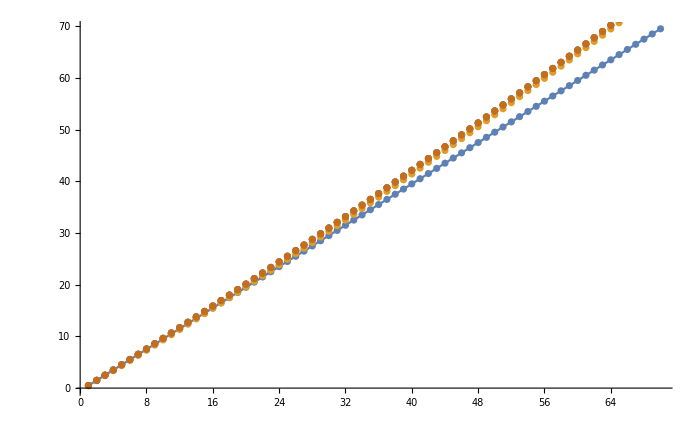

ListPlot::lpn: relativeEigenval is not a list of numbers or pairs of numbers.

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[relativeEigenval],ImageSize→700]

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.479489 | 1.44119 | 2.40831 | 3.38075 | 4.35843 | 5.34129 | 6.32924 | 7.32221 | 8.32013 | 9.32294 | 10.3306 | 11.343 | 12.36 | 13.3818 | 14.4081 | 15.4389 | 16.4742 | 17.514 | 18.5581 | 19.6065 | 20.6593 | 21.7162 | 22.7773 | 23.8426 | 24.912 | 25.9855 | 27.0629 | 28.1444 | 29.2298 | 30.3191 | 31.4123 | 32.5093 | 33.6101 | 34.7147 | 35.823 | 36.935 | 38.0506 | 39.17 | 40.2929 | 41.4194 | 42.5494 | 43.683 | 44.8201 | 45.9606 | 47.1046 | 48.252 | 49.4028 | 50.5569 | 51.7144 | 52.8752 | 54.0392 | 55.2066 | 56.3772 | 57.551 | 58.728 | 59.9082 | 61.0915 | 62.278 | 63.4676 | 64.6603 | 65.856 | 67.0548 | 68.2567 | 69.4615 | 70.6694 | 71.8802 | 73.094 | 74.3108 | 75.5305 | 76.753
0.498191 | 1.49657 | 2.49893 | 3.50523 | 4.51544 | 5.52954 | 6.54748 | 7.56925 | 8.5948 | 9.62412 | 10.6572 | 11.6939 | 12.7344 | 13.7785 | 14.8262 | 15.8775 | 16.9324 | 17.9909 | 19.0528 | 20.1183 | 21.1873 | 22.2597 | 23.3356 | 24.4149 | 25.4976 | 26.5836 | 27.673 | 28.7658 | 29.8618 | 30.9612 | 32.0638 | 33.1697 | 34.2789 | 35.3912 | 36.5068 | 37.6255 | 38.7474 | 39.8725 | 41.0006 | 42.132 | 43.2664 | 44.4039 | 45.5444 | 46.688 | 47.8347 | 48.9844 | 50.137 | 51.2927 | 52.4514 | 53.613 | 54.7776 | 55.9451 | 57.1155 | 58.2889 | 59.4651 | 60.6442 | 61.8262 | 63.0111 | 64.1988 | 65.3893 | 66.5826 | 67.7788 | 68.9778 | 70.1795 | 71.384 | 72.5913 | 73.8013 | 75.0141 | 76.2295 | 77.4477
0.497904 | 1.49573 | 2.49756 | 3.50337 | 4.51313 | 5.52679 | 6.54434 | 7.56573 | 8.59094 | 9.61994 | 10.6527 | 11.6892 | 12.7294 | 13.7732 | 14.8207 | 15.8719 | 16.9266 | 17.9849 | 19.0467 | 20.1121 | 21.181 | 22.2533 | 23.3291 | 24.4083 | 25.491 | 26.577 | 27.6664 | 28.7591 | 29.8551 | 30.9545 | 32.0572 | 33.1631 | 34.2722 | 35.3846 | 36.5002 | 37.619 | 38.7409 | 39.8661 | 40.9943 | 42.1257 | 43.2602 | 44.3978 | 45.5384 | 46.6821 | 47.8289 | 48.9787 | 50.1314 | 51.2872 | 52.446 | 53.6077 | 54.7724 | 55.94 | 57.1106 | 58.2841 | 59.4604 | 60.6397 | 61.8218 | 63.0068 | 64.1946 | 65.3852 | 66.5787 | 67.775 | 68.9741 | 70.176 | 71.3806 | 72.588 | 73.7981 | 75.011 | 76.2266 | 77.445
0.499024 | 1.49898 | 2.50275 | 3.5103 | 4.52162 | 5.53668 | 6.55546 | 7.57794 | 8.60411 | 9.63393 | 10.6674 | 11.7045 | 12.7451 | 13.7894 | 14.8372 | 15.8886 | 16.9434 | 18.0018 | 19.0636 | 20.129 | 21.1977 | 22.2699 | 23.3455 | 24.4244 | 25.5068 | 26.5925 | 27.6815 | 28.7739 | 29.8695 | 30.9684 | 32.0706 | 33.1761 | 34.2847 | 35.3966 | 36.5117 | 37.63 | 38.7514 | 39.876 | 41.0037 | 42.1346 | 43.2686 | 44.4056 | 45.5457 | 46.6889 | 47.8352 | 48.9844 | 50.1367 | 51.292 | 52.4503 | 53.6116 | 54.7758 | 55.943 | 57.1131 | 58.2861 | 59.4621 | 60.6409 | 61.8227 | 63.0073 | 64.1947 | 65.385 | 66.5782 | 67.7741 | 68.9729 | 70.1745 | 71.3789 | 72.586 | 73.7959 | 75.0086 | 76.224 | 77.4421
0.498536 | 1.49758 | 2.50057 | 3.50745 | 4.51821 | 5.53281 | 6.55121 | 7.5734 | 8.59933 | 9.62899 | 10.6624 | 11.6994 | 12.7401 | 13.7843 | 14.8322 | 15.8837 | 16.9387 | 17.9972 | 19.0592 | 20.1248 | 21.1937 | 22.2661 | 23.3419 | 24.4211 | 25.5037 | 26.5897 | 27.679 | 28.7715 | 29.8674 | 30.9666 | 32.069 | 33.1747 | 34.2836 | 35.3957 | 36.5111 | 37.6295 | 38.7512 | 39.876 | 41.0039 | 42.1349 | 43.269 | 44.4062 | 45.5465 | 46.6898 | 47.8362 | 48.9856 | 50.138 | 51.2933 | 52.4517 | 53.613 | 54.7773 | 55.9446 | 57.1147 | 58.2878 | 59.4638 | 60.6426 | 61.8244 | 63.009 | 64.1964 | 65.3867 | 66.5798 | 67.7758 | 68.9745 | 70.176 | 71.3803 | 72.5874 | 73.7973 | 75.0099 | 76.2252 | 77.4432

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.958978 | 0.960795 | 0.963323 | 0.965928 | 0.968541 | 0.971143 | 0.973729 | 0.976294 | 0.978839 | 0.981362 | 0.983864 | 0.986344 | 0.988803 | 0.991242 | 0.993661 | 0.99606 | 0.998439 | 1.0008 | 1.00314 | 1.00546 | 1.00777 | 1.01006 | 1.01233 | 1.01458 | 1.01682 | 1.01904 | 1.02124 | 1.02343 | 1.02561 | 1.02777 | 1.02991 | 1.03204 | 1.03416 | 1.03626 | 1.03835 | 1.04042 | 1.04248 | 1.04453 | 1.04657 | 1.04859 | 1.0506 | 1.0526 | 1.05459 | 1.05657 | 1.05853 | 1.06048 | 1.06242 | 1.06436 | 1.06628 | 1.06818 | 1.07008 | 1.07197 | 1.07385 | 1.07572 | 1.07758 | 1.07943 | 1.08127 | 1.0831 | 1.08492 | 1.08673 | 1.08853 | 1.09032 | 1.09211 | 1.09388 | 1.09565 | 1.09741 | 1.09916 | 1.1009 | 1.10263 | 1.10436
0.996383 | 0.997714 | 0.999571 | 1.00149 | 1.00343 | 1.00537 | 1.0073 | 1.00923 | 1.01115 | 1.01307 | 1.01497 | 1.01686 | 1.01875 | 1.02063 | 1.0225 | 1.02435 | 1.02621 | 1.02805 | 1.02988 | 1.03171 | 1.03353 | 1.03534 | 1.03714 | 1.03893 | 1.04072 | 1.0425 | 1.04427 | 1.04603 | 1.04778 | 1.04953 | 1.05127 | 1.05301 | 1.05473 | 1.05645 | 1.05817 | 1.05987 | 1.06157 | 1.06327 | 1.06495 | 1.06663 | 1.06831 | 1.06997 | 1.07163 | 1.07329 | 1.07494 | 1.07658 | 1.07822 | 1.07985 | 1.08147 | 1.08309 | 1.0847 | 1.08631 | 1.08791 | 1.08951 | 1.0911 | 1.09269 | 1.09427 | 1.09584 | 1.09741 | 1.09898 | 1.10054 | 1.10209 | 1.10364 | 1.10519 | 1.10673 | 1.10826 | 1.10979 | 1.11132 | 1.11284 | 1.11436
0.995807 | 0.99715 | 0.999024 | 1.00096 | 1.00292 | 1.00487 | 1.00682 | 1.00876 | 1.0107 | 1.01263 | 1.01454 | 1.01645 | 1.01835 | 1.02024 | 1.02212 | 1.02399 | 1.02585 | 1.02771 | 1.02955 | 1.03139 | 1.03322 | 1.03504 | 1.03685 | 1.03865 | 1.04045 | 1.04223 | 1.04401 | 1.04579 | 1.04755 | 1.04931 | 1.05105 | 1.0528 | 1.05453 | 1.05626 | 1.05798 | 1.05969 | 1.0614 | 1.0631 | 1.06479 | 1.06647 | 1.06815 | 1.06983 | 1.07149 | 1.07315 | 1.07481 | 1.07645 | 1.0781 | 1.07973 | 1.08136 | 1.08298 | 1.0846 | 1.08621 | 1.08782 | 1.08942 | 1.09102 | 1.09261 | 1.09419 | 1.09577 | 1.09734 | 1.09891 | 1.10047 | 1.10203 | 1.10359 | 1.10513 | 1.10668 | 1.10821 | 1.10975 | 1.11127 | 1.1128 | 1.11432
0.998048 | 0.999321 | 1.0011 | 1.00294 | 1.0048 | 1.00667 | 1.00853 | 1.01039 | 1.01225 | 1.0141 | 1.01594 | 1.01778 | 1.01961 | 1.02144 | 1.02326 | 1.02507 | 1.02687 | 1.02867 | 1.03047 | 1.03225 | 1.03403 | 1.03581 | 1.03758 | 1.03934 | 1.04109 | 1.04284 | 1.04459 | 1.04632 | 1.04805 | 1.04978 | 1.0515 | 1.05321 | 1.05491 | 1.05662 | 1.05831 | 1.06 | 1.06168 | 1.06336 | 1.06503 | 1.0667 | 1.06836 | 1.07001 | 1.07166 | 1.07331 | 1.07495 | 1.07658 | 1.07821 | 1.07983 | 1.08145 | 1.08306 | 1.08467 | 1.08627 | 1.08787 | 1.08946 | 1.09105 | 1.09263 | 1.09421 | 1.09578 | 1.09735 | 1.09891 | 1.10047 | 1.10202 | 1.10357 | 1.10511 | 1.10665 | 1.10818 | 1.10971 | 1.11124 | 1.11276 | 1.11427
0.997073 | 0.99839 | 1.00023 | 1.00213 | 1.00405 | 1.00596 | 1.00788 | 1.00979 | 1.01169 | 1.01358 | 1.01546 | 1.01734 | 1.0192 | 1.02106 | 1.02291 | 1.02475 | 1.02659 | 1.02841 | 1.03023 | 1.03204 | 1.03384 | 1.03563 | 1.03742 | 1.0392 | 1.04097 | 1.04273 | 1.04449 | 1.04624 | 1.04798 | 1.04972 | 1.05144 | 1.05317 | 1.05488 | 1.05659 | 1.05829 | 1.05999 | 1.06168 | 1.06336 | 1.06504 | 1.06671 | 1.06837 | 1.07003 | 1.07168 | 1.07333 | 1.07497 | 1.07661 | 1.07824 | 1.07986 | 1.08148 | 1.08309 | 1.0847 | 1.0863 | 1.0879 | 1.08949 | 1.09108 | 1.09266 | 1.09424 | 1.09581 | 1.09737 | 1.09894 | 1.10049 | 1.10204 | 1.10359 | 1.10513 | 1.10667 | 1.1082 | 1.10973 | 1.11126 | 1.11278 | 1.11429

```mathematica
Carbon - look at harmonic and anharmonic eigenvalues;
(*Omega=31.58754341976066;M=12;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)
cOmega0=31.58754341976066;
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues}],ListPlot@eigenEnergies,ImageSize->700]
Show[ListPlot@relativeEigenval,ImageSize->700]
relativeEigenval=Table[eigensysC[[k]][[1]]/eigensysC[[1]][[1]],{k,1,6}];
eigenEnergies//TableForm
relativeEigenval//TableForm
```

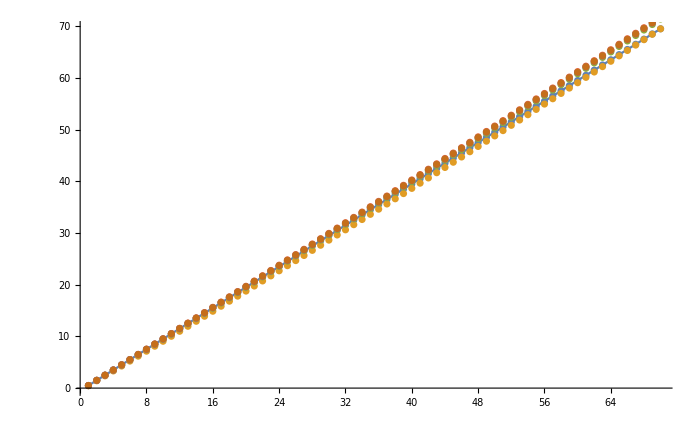

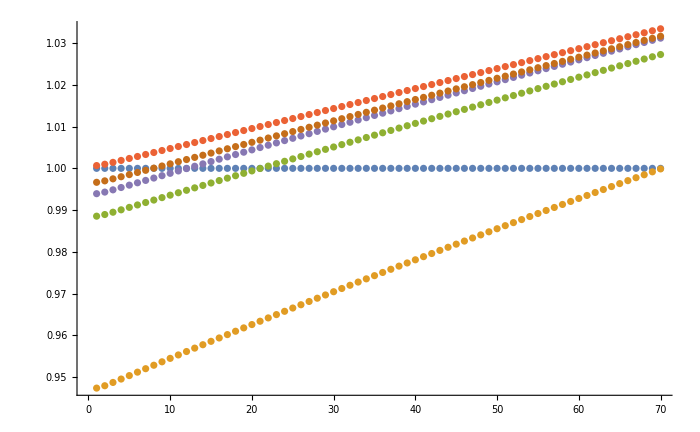

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5001 | 68.5001 | 69.5001
0.47367 | 1.42185 | 2.37173 | 3.32328 | 4.2765 | 5.23139 | 6.18793 | 7.14612 | 8.10595 | 9.0674 | 10.0305 | 10.9952 | 11.9615 | 12.9294 | 13.8989 | 14.87 | 15.8426 | 16.8169 | 17.7927 | 18.77 | 19.7489 | 20.7294 | 21.7114 | 22.6949 | 23.68 | 24.6665 | 25.6546 | 26.6442 | 27.6352 | 28.6278 | 29.6219 | 30.6174 | 31.6144 | 32.6129 | 33.6129 | 34.6143 | 35.6171 | 36.6214 | 37.6271 | 38.6343 | 39.6429 | 40.6529 | 41.6644 | 42.6772 | 43.6915 | 44.7071 | 45.7242 | 46.7426 | 47.7625 | 48.7837 | 49.8063 | 50.8303 | 51.8556 | 52.8823 | 53.9103 | 54.9397 | 55.9705 | 57.0025 | 58.036 | 59.0707 | 60.1068 | 61.1442 | 62.183 | 63.223 | 64.2644 | 65.307 | 66.351 | 67.3962 | 68.4428 | 69.4906
0.494269 | 1.4834 | 2.47372 | 3.46522 | 4.4579 | 5.45176 | 6.4468 | 7.44301 | 8.44039 | 9.43893 | 10.4386 | 11.4395 | 12.4416 | 13.4447 | 14.4491 | 15.4546 | 16.4612 | 17.469 | 18.478 | 19.488 | 20.4992 | 21.5116 | 22.5251 | 23.5397 | 24.5554 | 25.5723 | 26.5903 | 27.6094 | 28.6297 | 29.651 | 30.6735 | 31.6971 | 32.7218 | 33.7476 | 34.7745 | 35.8025 | 36.8316 | 37.8618 | 38.8931 | 39.9255 | 40.959 | 41.9936 | 43.0293 | 44.066 | 45.1039 | 46.1428 | 47.1828 | 48.2239 | 49.266 | 50.3093 | 51.3535 | 52.3989 | 53.4453 | 54.4928 | 55.5414 | 56.591 | 57.6417 | 58.6934 | 59.7462 | 60.8 | 61.8549 | 62.9109 | 63.9679 | 65.0259 | 66.085 | 67.1451 | 68.2062 | 69.2684 | 70.3316 | 71.3959
0.500333 | 1.50148 | 2.50358 | 3.50664 | 4.51067 | 5.51565 | 6.52159 | 7.52849 | 8.53635 | 9.54517 | 10.5549 | 11.5657 | 12.5774 | 13.59 | 14.6036 | 15.6182 | 16.6338 | 17.6503 | 18.6677 | 19.6861 | 20.7055 | 21.7258 | 22.7471 | 23.7694 | 24.7926 | 25.8167 | 26.8418 | 27.8679 | 28.895 | 29.923 | 30.9519 | 31.9818 | 33.0127 | 34.0445 | 35.0773 | 36.111 | 37.1457 | 38.1814 | 39.218 | 40.2555 | 41.294 | 42.3335 | 43.3739 | 44.4153 | 45.4576 | 46.5009 | 47.5451 | 48.5903 | 49.6365 | 50.6835 | 51.7316 | 52.7806 | 53.8305 | 54.8814 | 55.9332 | 56.986 | 58.0398 | 59.0945 | 60.1501 | 61.2067 | 62.2642 | 63.3227 | 64.3821 | 65.4425 | 66.5038 | 67.566 | 68.6292 | 69.6934 | 70.7584 | 71.8245
0.496964 | 1.49147 | 2.48712 | 3.48393 | 4.48188 | 5.48097 | 6.4812 | 7.48257 | 8.48507 | 9.4887 | 10.4934 | 11.4993 | 12.5063 | 13.5144 | 14.5237 | 15.534 | 16.5454 | 17.558 | 18.5716 | 19.5864 | 20.6022 | 21.6191 | 22.6372 | 23.6563 | 24.6765 | 25.6977 | 26.7201 | 27.7435 | 28.768 | 29.7936 | 30.8203 | 31.848 | 32.8767 | 33.9066 | 34.9375 | 35.9694 | 37.0024 | 38.0365 | 39.0716 | 40.1077 | 41.1449 | 42.1832 | 43.2225 | 44.2628 | 45.3041 | 46.3465 | 47.3899 | 48.4344 | 49.4798 | 50.5263 | 51.5739 | 52.6224 | 53.6719 | 54.7225 | 55.7741 | 56.8267 | 57.8803 | 58.9349 | 59.9906 | 61.0472 | 62.1048 | 63.1635 | 64.2231 | 65.2837 | 66.3454 | 67.408 | 68.4716 | 69.5362 | 70.6018 | 71.6684
0.498328 | 1.4955 | 2.49371 | 3.49296 | 4.49325 | 5.49458 | 6.49694 | 7.50033 | 8.50477 | 9.51023 | 10.5167 | 11.5243 | 12.5328 | 13.5424 | 14.5531 | 15.5647 | 16.5774 | 17.5911 | 18.6059 | 19.6217 | 20.6385 | 21.6563 | 22.6751 | 23.695 | 24.7159 | 25.7378 | 26.7608 | 27.7848 | 28.8097 | 29.8357 | 30.8628 | 31.8908 | 32.9199 | 33.9499 | 34.981 | 36.0131 | 37.0463 | 38.0804 | 39.1155 | 40.1517 | 41.1888 | 42.227 | 43.2662 | 44.3063 | 45.3475 | 46.3897 | 47.4329 | 48.4771 | 49.5223 | 50.5685 | 51.6157 | 52.6638 | 53.713 | 54.7632 | 55.8144 | 56.8665 | 57.9197 | 58.9739 | 60.029 | 61.0851 | 62.1422 | 63.2003 | 64.2594 | 65.3195 | 66.3806 | 67.4426 | 68.5056 | 69.5696 | 70.6346 | 71.7006

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.947339 | 0.947903 | 0.948691 | 0.949509 | 0.950334 | 0.951162 | 0.951989 | 0.952816 | 0.953641 | 0.954464 | 0.955284 | 0.956103 | 0.956919 | 0.957733 | 0.958544 | 0.959353 | 0.96016 | 0.960964 | 0.961766 | 0.962566 | 0.963363 | 0.964158 | 0.96495 | 0.965741 | 0.966529 | 0.967314 | 0.968098 | 0.968879 | 0.969658 | 0.970434 | 0.971209 | 0.971981 | 0.972752 | 0.97352 | 0.974285 | 0.975049 | 0.975811 | 0.976571 | 0.977328 | 0.978084 | 0.978837 | 0.979588 | 0.980338 | 0.981085 | 0.981831 | 0.982574 | 0.983316 | 0.984055 | 0.984793 | 0.985529 | 0.986263 | 0.986995 | 0.987725 | 0.988453 | 0.98918 | 0.989904 | 0.990627 | 0.991348 | 0.992067 | 0.992785 | 0.9935 | 0.994214 | 0.994927 | 0.995637 | 0.996346 | 0.997053 | 0.997758 | 0.998462 | 0.999164 | 0.999864
0.988537 | 0.988933 | 0.989487 | 0.990063 | 0.990645 | 0.99123 | 0.991815 | 0.992401 | 0.992987 | 0.993572 | 0.994157 | 0.994741 | 0.995324 | 0.995907 | 0.996489 | 0.99707 | 0.99765 | 0.99823 | 0.998808 | 0.999386 | 0.999963 | 1.00054 | 1.00111 | 1.00169 | 1.00226 | 1.00284 | 1.00341 | 1.00398 | 1.00455 | 1.00512 | 1.00569 | 1.00626 | 1.00682 | 1.00739 | 1.00796 | 1.00852 | 1.00909 | 1.00965 | 1.01021 | 1.01077 | 1.01133 | 1.01189 | 1.01245 | 1.01301 | 1.01357 | 1.01413 | 1.01468 | 1.01524 | 1.01579 | 1.01635 | 1.0169 | 1.01745 | 1.01801 | 1.01856 | 1.01911 | 1.01966 | 1.02021 | 1.02075 | 1.0213 | 1.02185 | 1.0224 | 1.02294 | 1.02349 | 1.02403 | 1.02457 | 1.02511 | 1.02566 | 1.0262 | 1.02674 | 1.02728
1.00067 | 1.00099 | 1.00143 | 1.0019 | 1.00237 | 1.00285 | 1.00332 | 1.0038 | 1.00428 | 1.00475 | 1.00523 | 1.00571 | 1.00619 | 1.00667 | 1.00715 | 1.00763 | 1.00811 | 1.00859 | 1.00906 | 1.00954 | 1.01002 | 1.0105 | 1.01098 | 1.01146 | 1.01194 | 1.01242 | 1.0129 | 1.01338 | 1.01386 | 1.01434 | 1.01482 | 1.0153 | 1.01577 | 1.01625 | 1.01673 | 1.01721 | 1.01769 | 1.01817 | 1.01865 | 1.01913 | 1.01961 | 1.02008 | 1.02056 | 1.02104 | 1.02152 | 1.022 | 1.02248 | 1.02295 | 1.02343 | 1.02391 | 1.02439 | 1.02487 | 1.02534 | 1.02582 | 1.0263 | 1.02677 | 1.02725 | 1.02773 | 1.02821 | 1.02868 | 1.02916 | 1.02964 | 1.03011 | 1.03059 | 1.03107 | 1.03154 | 1.03202 | 1.03249 | 1.03297 | 1.03344
0.993927 | 0.994312 | 0.99485 | 0.995409 | 0.995973 | 0.996541 | 0.997108 | 0.997676 | 0.998243 | 0.99881 | 0.999376 | 0.999941 | 1.00051 | 1.00107 | 1.00163 | 1.00219 | 1.00275 | 1.00331 | 1.00387 | 1.00443 | 1.00499 | 1.00554 | 1.0061 | 1.00665 | 1.0072 | 1.00775 | 1.00831 | 1.00886 | 1.0094 | 1.00995 | 1.0105 | 1.01105 | 1.01159 | 1.01214 | 1.01268 | 1.01322 | 1.01376 | 1.01431 | 1.01485 | 1.01539 | 1.01592 | 1.01646 | 1.017 | 1.01753 | 1.01807 | 1.0186 | 1.01914 | 1.01967 | 1.0202 | 1.02073 | 1.02126 | 1.02179 | 1.02232 | 1.02285 | 1.02338 | 1.0239 | 1.02443 | 1.02496 | 1.02548 | 1.026 | 1.02653 | 1.02705 | 1.02757 | 1.02809 | 1.02861 | 1.02913 | 1.02965 | 1.03017 | 1.03068 | 1.0312
0.996655 | 0.997001 | 0.997486 | 0.99799 | 0.998501 | 0.999014 | 0.999529 | 1.00004 | 1.00056 | 1.00108 | 1.00159 | 1.00211 | 1.00263 | 1.00314 | 1.00366 | 1.00418 | 1.00469 | 1.00521 | 1.00572 | 1.00624 | 1.00675 | 1.00727 | 1.00778 | 1.0083 | 1.00881 | 1.00933 | 1.00984 | 1.01035 | 1.01087 | 1.01138 | 1.01189 | 1.01241 | 1.01292 | 1.01343 | 1.01394 | 1.01445 | 1.01497 | 1.01548 | 1.01599 | 1.0165 | 1.01701 | 1.01752 | 1.01803 | 1.01854 | 1.01905 | 1.01955 | 1.02006 | 1.02057 | 1.02108 | 1.02158 | 1.02209 | 1.0226 | 1.0231 | 1.02361 | 1.02412 | 1.02462 | 1.02513 | 1.02563 | 1.02614 | 1.02664 | 1.02714 | 1.02765 | 1.02815 | 1.02865 | 1.02916 | 1.02966 | 1.03016 | 1.03066 | 1.03116 | 1.03166

```mathematica
Zirconium - look at harmonic and anharmonic eigenvalues;
(*zOmega=13.44788050977517;M=91;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)
zOmega0=13.44788050977517;
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];
Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues}],ListPlot@eigenEnergiesZ,ImageSize->700]
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
Show[ListPlot@relativeEigenvalz,ImageSize->700]
eigenEnergiesZ//TableForm
relativeEigenvalz//TableForm
```

{1.,1.10436,1.11436,1.11432,1.11427,1.11429}

{1.,0.999864,1.02728,1.03344,1.0312,1.03166}

{ImageSize→600,PlotLegends→SwatchLegend[{10th,20th,30th,40th,50th,60th,70th}],PlotLabel→Convergence of eigenvalues with fit order,AxesLabel→{1/2(Fit Order),Anharmonicity}}

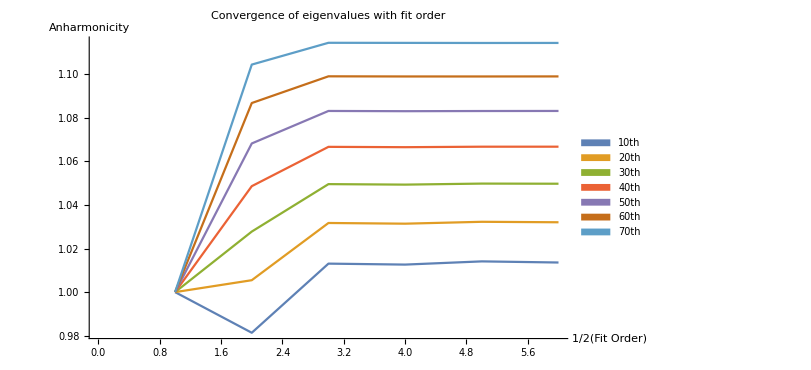

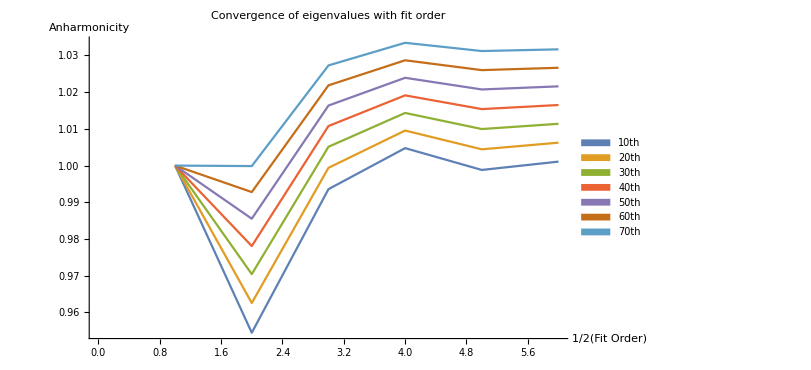

```mathematica
Carbon and zirconium - check convergence of eigenvalues with fit order;
Transpose[relativeEigenval][[70]]
Transpose[relativeEigenvalz][[70]]
plotstuff={ImageSize->600,PlotLegends->SwatchLegend[{"10th","20th","30th","40th","50th","60th","70th"}],PlotLabel->"Convergence of eigenvalues with fit order",AxesLabel->{"1/2(Fit Order)","Anharmonicity"}}
ListPlot[Table[Transpose[relativeEigenval][[i]],{i,10,70,10}], Joined->True,plotstuff]
ListPlot[Table[Transpose[relativeEigenvalz][[i]],{i,10,70,10}], Joined->True,plotstuff]
```

```mathematica
Plot input stuff for eigenvalues times wavefunctions  for different order potentials;
eigenPlots=Table[Show[Plot[Evaluate[(6*eigensysC[[i]][[2]])+eigensysC[[i]][[1]]],{x,-B,B}],Plot[Evaluate@V[1,2i,x],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
```

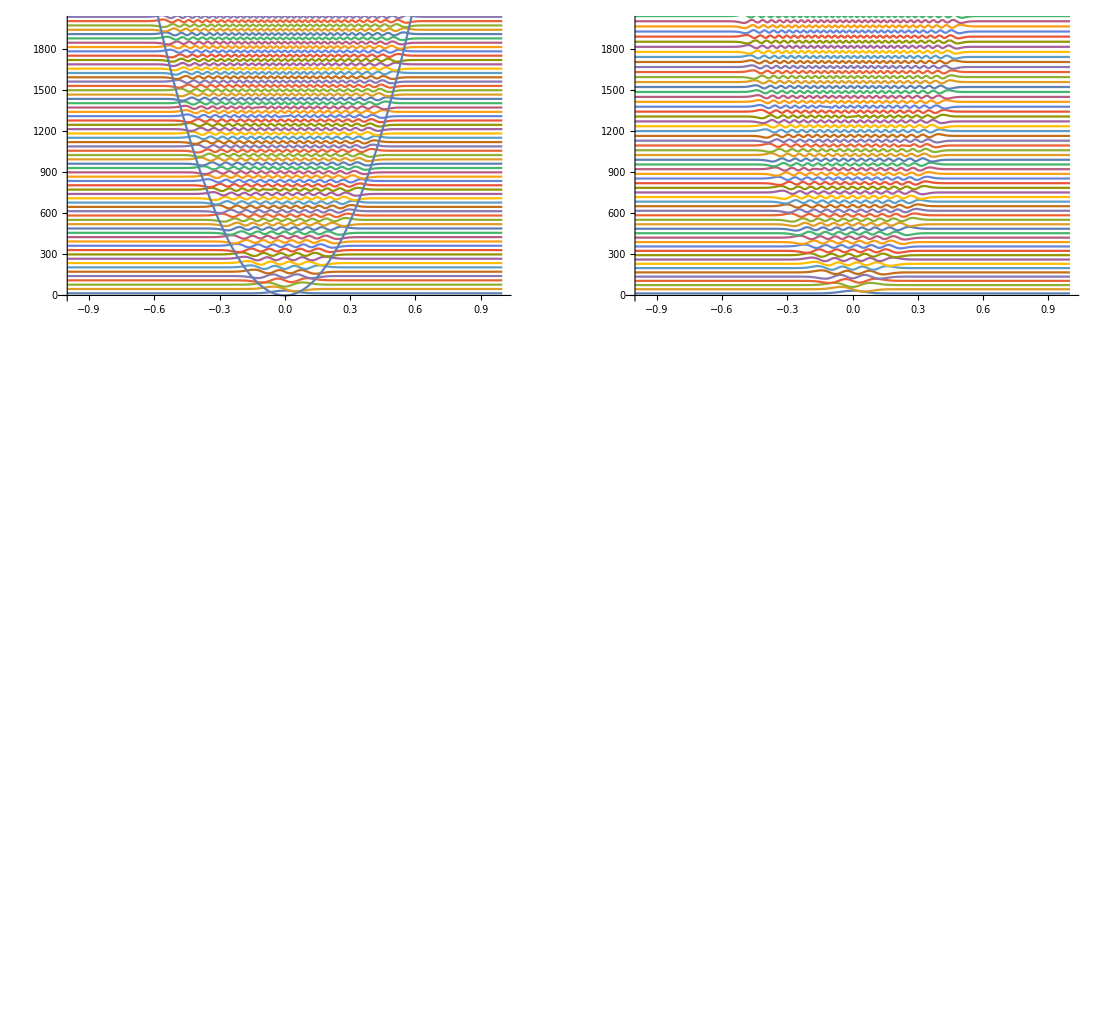

```mathematica
Plot carbon eigensystem;
GraphicsGrid[plotgrid,ImageSize->1100]
```

```mathematica
Plot input stuff for eigenvalues times wavefunctions  for different order potentials;
Bz=0.5;Hz=1000;
eigenPlotsz=Table[Show[Plot[Evaluate[(4*eigensysZ[[i]][[2]])+eigensysZ[[i]][[1]]],{x,-Bz,Bz}],Plot[Evaluate@V[2,2i,x],{x,-Bz,Bz}],PlotRange->{{-Bz,Bz},{0,Hz}},AxesOrigin->{-Bz,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
plotgridz={Table[eigenPlotsz[[i]],{i,1,2}],Table[eigenPlotsz[[j]],{j,3,4}],Table[eigenPlotsz[[k]],{k,5,6}]};
```

$Aborted

Part::partd: Part specification eigenPlotsz⟦1⟧ is longer than depth of object.

Part::partd: Part specification eigenPlotsz⟦2⟧ is longer than depth of object.

Part::partd: Part specification eigenPlotsz⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Plot zirconium eigensystem;
GraphicsGrid[plotgridz,ImageSize->1100]
```

-Graphics-

```mathematica
Carbon - Look at how well a linear fit approximate the anharmonic perturbation from a 12th order potential
(*Make a function*)
anharmonicfit1=Fit[relativeEigenval[[5]],{1,x},x]
anharmonicfit2=Fit[relativeEigenval[[5]],{1, x, x^2},x]
anharmonicfit3=Fit[relativeEigenval[[5]],{1, x, x^2,x^3},x]
anharmonicfit4=Fit[relativeEigenval[[5]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenval[[5]]],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ImageSize->900]
```

Carbon-12 a^2 anharmonic approximate at fit from how linear Look order perturbation potential th the well

0.997916+0.00169246 x

0.995552+0.00188943 x-2.77422×10^-6 x^2

0.995549+0.00189 x-2.79437×10^-6 x^2+1.8919×10^-10 x^3

0.995692+0.00185206 x-4.29005×10^-7 x^2-5.13864×10^-8 x^3+3.63208×10^-10 x^4

-Graphics-

```mathematica
Zirconium - Look at how well a linear fit approximate the anharmonic perturbation from a 12th order potential
(*Make a function*)
anharmonicfit1z=Fit[relativeEigenvalz[[6]],{1,x},x]
anharmonicfit2z=Fit[relativeEigenvalz[[6]],{1, x, x^2},x]
anharmonicfit3z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3},x]
anharmonicfit4z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenvalz[[6]]],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

-12 a^2 anharmonic approximate at fit from how linear Look order perturbation potential th the well+Zirconium

0.996021+0.000510629 x

0.995932+0.000518036 x-1.04332×10^-7 x^2

0.995977+0.000510718 x+1.51536×10^-7 x^2-2.40252×10^-9 x^3

0.996018+0.000499913 x+8.25116×10^-7 x^2-1.70896×10^-8 x^3+1.0343×10^-10 x^4

-Graphics-

```mathematica
Show[ListPlot[relativeEigenval[[5]]],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ListPlot[relativeEigenvalz[[6]]],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
cForceCorrection=D[{anharmonicfit1,anharmonicfit2,anharmonicfit3,anharmonicfit4},x]
zForceCorrection=D[{anharmonicfit1z,anharmonicfit2z,anharmonicfit3z,anharmonicfit4z},x]
GraphicsGrid[{{Show@Plot[{cForceCorrection},{x,0,70}],Show@Plot[{zForceCorrection},{x,0,70}]}}]
```

-Graphics-

{0.00169246,0.00188943-5.54844×10^-6 x,0.00189-5.58874×10^-6 x+5.67571×10^-10 x^2,0.00185206-8.58009×10^-7 x-1.54159×10^-7 x^2+1.45283×10^-9 x^3}

{0.000510629,0.000518036-2.08663×10^-7 x,0.000510718+3.03072×10^-7 x-7.20755×10^-9 x^2,0.000499913+1.65023×10^-6 x-5.12687×10^-8 x^2+4.1372×10^-10 x^3}

-Graphics-

```mathematica
(*Assume linear anharmonic force correction*)
cForceCorrection[[2]]
(*Then Hessian correction as:*)
D[cForceCorrection[[2]],x]
```

0.00188943-5.54844×10^-6 x

-5.54844×10^-6

```mathematica
(*Calculate partition function and Helmholtz free energy*)
(*As previous, define omega0 as the solution to A*x*x=1/2*m*omega*omega*x*x, where A*x*x is the harmonic fit*)
"4.685Ang Einstein frequencies from polynomial fit:"
Acarbon=V[1,2,X][[1]];
cOmega0=Sqrt[2Acarbon/m[[1]]]
Azirconium=V[2,2,X][[1]];
zOmega0=Sqrt[2Azirconium/m[[2]]] 
(*Note, if we define the Einstein frequency in terms of the QHA DOS as the energy integrating up to which gives the number of modes equal to the 3*Natoms/2, then the frequencies are*)
"4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:"
cOmegaInt48=65.1879672429008/2
zrOmegaInt48=26.329538754361874/2
"4.685Ang Einstein frequencies from QHA finding peak frequency for each band:"
cOmegaMaxPeak=4.14*18.0295229515/2
zrOmegaMaxPeak=4.14*6.2446881878/2
```

4.685Ang Einstein frequencies from polynomial fit:

31.5875

13.4479

4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:

32.594

13.1648

4.685Ang Einstein frequencies from QHA finding peak frequency for each band:

37.3211

12.9265

```mathematica
perfectHarmonic=Table[0.5+i,{i,0,70}];
Partition[perfectHarmonic,15]//TableForm
Partition[eigenEnergiesZ[[1]],15]//TableForm
Partition[eigenEnergiesZ[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.498328 | 1.4955 | 2.49371 | 3.49296 | 4.49325 | 5.49458 | 6.49694 | 7.50033 | 8.50477 | 9.51023 | 10.5167 | 11.5243 | 12.5328 | 13.5424 | 14.5531
15.5647 | 16.5774 | 17.5911 | 18.6059 | 19.6217 | 20.6385 | 21.6563 | 22.6751 | 23.695 | 24.7159 | 25.7378 | 26.7608 | 27.7848 | 28.8097 | 29.8357
30.8628 | 31.8908 | 32.9199 | 33.9499 | 34.981 | 36.0131 | 37.0463 | 38.0804 | 39.1155 | 40.1517 | 41.1888 | 42.227 | 43.2662 | 44.3063 | 45.3475
46.3897 | 47.4329 | 48.4771 | 49.5223 | 50.5685 | 51.6157 | 52.6638 | 53.713 | 54.7632 | 55.8144 | 56.8665 | 57.9197 | 58.9739 | 60.029 | 61.0851

```mathematica
ZperfectHarmonic[T_]:=Total[Exp[-(zOmega0*perfectHarmonic)/(kB*T)]]
Zzr12thfit[T_]:=Total[Exp[-(zOmega0*eigenEnergiesZ[[6]])/(kB*T)]]
```

```mathematica
perfect[T_]:=Exp[-perfectHarmonic/(kB*T)]
zr12thfit[T_]:=Exp[-eigenEnergiesZ[[6]]/(kB*T)]

probPerf[T_]:=(1/ZperfectHarmonic[T])*perfect[T]
prob12thFit[T_]:=(1/Zzr12thfit[T])*zr12thfit[T]
```

```mathematica
probPerf[4000]
prob12thFit[400]
```

{0.386965,0.3759,0.365152,0.35471,0.344568,0.334715,0.325144,0.315846,0.306815,0.298042,0.289519,0.281241,0.273199,0.265387,0.257798,0.250427,0.243266,0.23631,0.229553,0.222989,0.216612,0.210418,0.204402,0.198557,0.192879,0.187364,0.182006,0.176802,0.171746,0.166835,0.162065,0.157431,0.152929,0.148556,0.144308,0.140182,0.136173,0.13228,0.128497,0.124823,0.121253,0.117786,0.114418,0.111147,0.107968,0.104881,0.101882,0.0989688,0.0961388,0.0933898,0.0907193,0.0881252,0.0856053,0.0831575,0.0807797,0.0784698,0.076226,0.0740464,0.071929,0.0698723,0.0678743,0.0659335,0.0640481,0.0622167,0.0604376,0.0587095,0.0570307,0.0553999,0.0538158,0.052277,0.0507821}

{5.92368,4.43561,3.32035,2.48476,1.85889,1.39025,1.03944,0.776923,0.58053,0.433652,0.323838,0.24176,0.180431,0.134619,0.100409,0.0748703,0.0558106,0.0415904,0.0309842,0.0230759,0.017181,0.0127881,0.00951561,0.00707844,0.00526393,0.00391339,0.00290849,0.00216099,0.00160513,0.0011919,0.00088479,0.000656618,0.000487143,0.000361304,0.000267893,0.000198574,0.000147148,0.000109009,0.0000807308,0.000059771,0.0000442399,0.0000327349,0.0000242148,0.0000179071,0.0000132386,9.78435×10^-6,7.2293×10^-6,5.33991×10^-6,3.94317×10^-6,2.91093×10^-6,2.14828×10^-6,1.58499×10^-6,1.16905×10^-6,8.6202×10^-7,6.35441×10^-7,4.68282×10^-7,3.44997×10^-7,2.54096×10^-7,1.87093×10^-7,1.37718×10^-7,1.01344×10^-7,7.45563×10^-8,5.48334×10^-8,4.03164×10^-8,2.96343×10^-8,2.17762×10^-8,1.59974×10^-8,1.17487×10^-8,8.62598×10^-9,6.33146×10^-9}

```mathematica
ListPlot[Table[probPerf[T],{T,1,4000,25}],Joined->True,ImageSize->700,AxesLabel->{"Temp (K)","Probability"},PlotLabel->"Perfect harmonic Zr Einstein oscillator"]
```

-Graphics-

```mathematica
ListPlot[Table[prob12thFit[T],{T,1,4000,25}],Joined->True,ImageSize->700,AxesLabel->{"Temp (K)","Probability"},PlotLabel->"12th order fit to anharmonic \n uncoupled Zr Einstein oscillator"]
```

-Graphics-

```mathematica
HelmholtzFreePerf[T_]:=-kB*T*Log[ZperfectHarmonic[T]]
HelmholtzFree12fit[T_]:=-kB*T*Log[Zzr12thfit[T]]
```

```mathematica
p1=Plot[{HelmholtzFreePerf[T],HelmholtzFree12fit[T]},{T,1,4000},ImageSize->400];
p2=Plot[{HelmholtzFreePerf[T],HelmholtzFree12fit[T]},{T,1,1000},ImageSize->400];
p3=Plot[{HelmholtzFreePerf[T],HelmholtzFree12fit[T]},{T,1,400},ImageSize->400];
GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
HelmholtzFree12fit[T_]:=-kB*T*Log[Zzr12thfit[T]]
```

```mathematica
probability[T_]:=(1/Z[T])*prefactor[T]
Z[4000];
probability[4000];
ListPlot[probability[1000],Joined->True];
HelmholtzFree[T_]:=-kB*T*Log[Z[T]]
Plot[HelmholtzFree[T],{T,1,10000}]
HelmholtzFree[10000]
```